### Start choosing the example:

```mathematica
t=1;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1},Adjacency Matrix→{{0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{1,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.011953,Null}

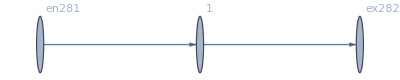

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1,Norm[{}]]

<|j283→80,j284→80,j285→0.,j286→0.,jt287→80,jt288→0.,u289→15.,u290→15.,u291→15.,u292→15.|>